# Lab 10-2

#### Approximate Sin[0.3] by 3 degree Taylor series centered at x=0

```mathematica
T3[x_]=Series[Sin[x],{x,0,3}]//Normal
```

x-x^3/6

```mathematica
T3[0.3]
```

0.2955

#### Q1: Approximate e^2 by 5th order Taylor polynomial centered at x=1

```mathematica
Q1T[x_]=Series[Exp[2x],{x,1,5}]
```

ⅇ^2+2 ⅇ^2 (x-1)+2 ⅇ^2 (x-1)^2+4/3 ⅇ^2 (x-1)^3+2/3 ⅇ^2 (x-1)^4+4/15 ⅇ^2 (x-1)^5+O[x-1]^6

```mathematica
Q1T[1]
```

ⅇ^2

#### Error Estimate of Cos[x]

```mathematica
Table[{n,((Pi/4.)^(n+1))/((n+1)!)},{n,4,8}]//TableForm//N
```

4. | 0.00249039
5. | 0.000325992
6. | 0.0000365762
7. | 3.59086×10^-6
8. | 3.13362×10^-7

Choose n to be at least 6

```mathematica
T6[x_]=Series[Cos[x],{x,Pi/4,6}]//Normal
```

1/(√2)-(-π/4+x)/(√2)-(-π/4+x)^2/(2 √2)+(-π/4+x)^3/(6 √2)+(-π/4+x)^4/(24 √2)-(-π/4+x)^5/(120 √2)-(-π/4+x)^6/(720 √2)

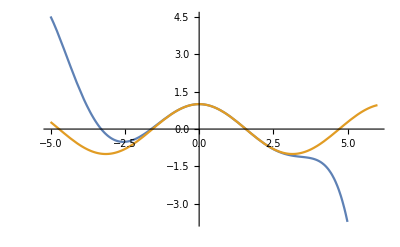

```mathematica
Plot[{T6[x],Cos[x]},{x,-5,6}]
```

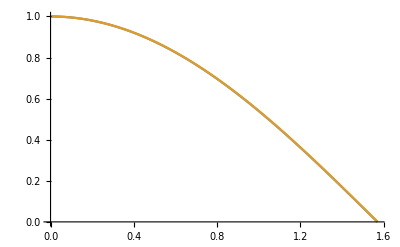

```mathematica
Plot[{T6[x],Cos[x]},{x,0,Pi/2}]
```

#### Q3: Find polynomial approximation to f(x)=e^x centered at x=0 in [-2,2] with error less than 0.005

```mathematica
M=Exp[2]
```

ⅇ^2

```mathematica
Table[{n,(Exp[2]*(2)^(n+1))/((n+1)!)},{n,8,12}]//TableForm//N
```

8. | 0.0104255
9. | 0.0020851
10. | 0.000379108
11. | 0.0000631847
12. | 9.72072×10^-6

Choose n to be at least 10

```mathematica
Q3T[x_]=Series[Exp[x],{x,0,10}]//Normal
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800

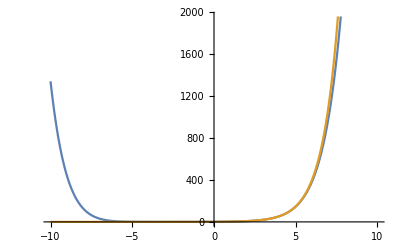

```mathematica
Plot[{Q3T[x],Exp[x]},{x,-10,10}]
```